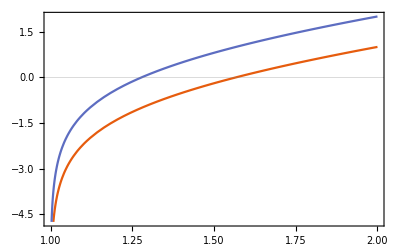

```mathematica
Plot[{r-1+Log[r-1],r+Log[r-1]},{r,1,2},PlotTheme->"Scientific"]
```

```mathematica
FullSimplify[-2rg ⅇ^(-ut/(2rg))/.ut->t-rstr/.rstr->r-rg+rg Log[r/rg-1],Assumptions->r>rg&&rg>0]
FullSimplify[2rg ⅇ^(vt/(2rg))/.vt->t+rstr/.rstr->r-rg+rg Log[r/rg-1],Assumptions->r>rg&&rg>0]
```

-2 ⅇ^(-(-r+rg+t)/(2 rg)) √((r-rg) rg)

2 ⅇ^((r-rg+t)/(2 rg)) √((r-rg) rg)

```mathematica
InverseFunction[# ⅇ^#&]
%//TraditionalForm
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

ProductLog[#1]&

W(#1)&

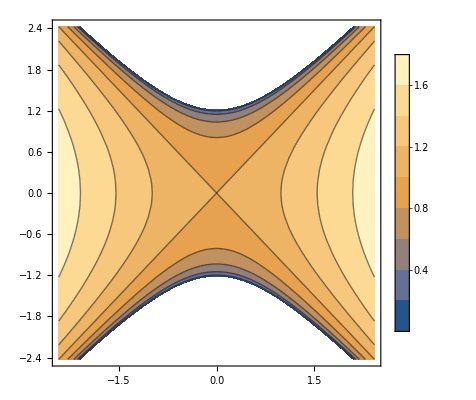

Power::infy: Infinite expression 1/0. encountered.

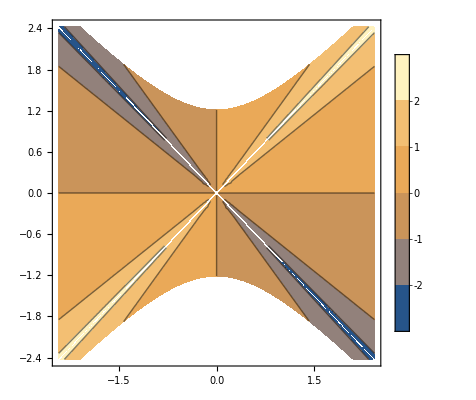

```mathematica
ContourPlot[1+ProductLog[-(T^2-R^2)/4],{R,-2 2/(√ⅇ),2 2/(√ⅇ)},{T,-2 2/(√ⅇ),2 2/(√ⅇ)},RegionFunction->Function[{R,T},T^2-R^2<4/ⅇ],PlotLegends->Automatic]
ContourPlot[1/2 Log[((T+R)/(T-R))^2],{R,-2 2/(√ⅇ),2 2/(√ⅇ)},{T,-2 2/(√ⅇ),2 2/(√ⅇ)},Exclusions->{T==R,T==-R},RegionFunction->Function[{R,T},T^2-R^2<4/ⅇ](*(#2^2-#1^2<1)&*),PlotLegends->Automatic]
```

```mathematica
(#2^2-#1^2<1)&[1,1]
```

True

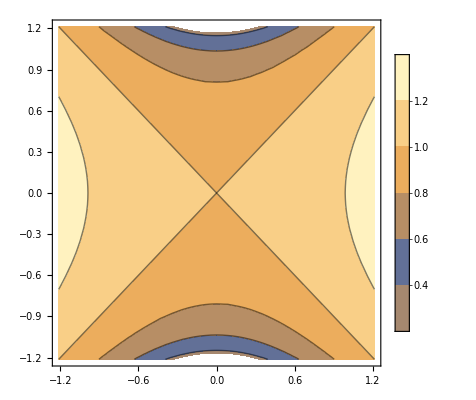

Power::infy: Infinite expression 1/0. encountered.

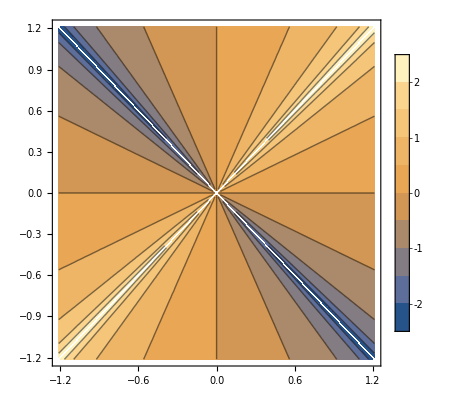

```mathematica
ContourPlot[1+ProductLog[-(T^2-R^2)/4],{R,-2/(√ⅇ),2/(√ⅇ)},{T,-2/(√ⅇ),2/(√ⅇ)},PlotLegends->Automatic]
ContourPlot[1/2 Log[((T+R)/(T-R))^2],{R,-2/(√ⅇ),2/(√ⅇ)},{T,-2/(√ⅇ),2/(√ⅇ)},Exclusions->Abs[T]==Abs[R],RegionFunction->Function[{R,T},T^2-R^2<4/ⅇ](*(#2^2-#1^2<1)&*),PlotLegends->Automatic]
```

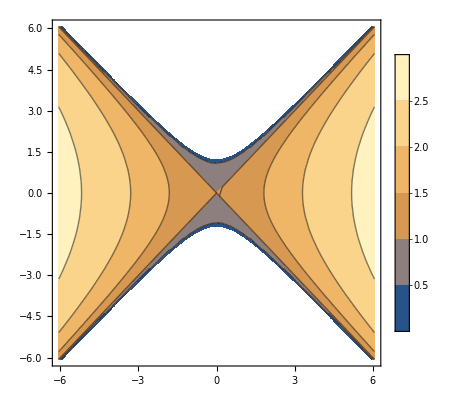

Power::infy: Infinite expression 1/0. encountered.

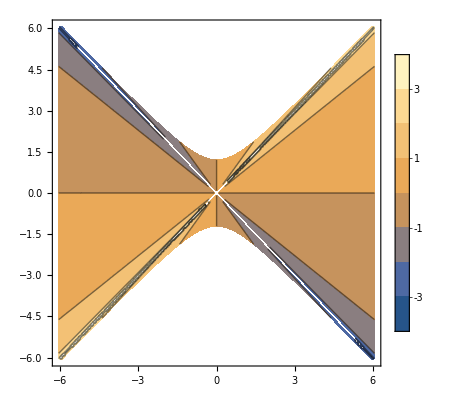

```mathematica
ContourPlot[1+ProductLog[-(T^2-R^2)/4],{R,-5 2/(√ⅇ),5 2/(√ⅇ)},{T,-5 2/(√ⅇ),5 2/(√ⅇ)},PlotLegends->Automatic]
ContourPlot[1/2 Log[((T+R)/(T-R))^2],{R,-5 2/(√ⅇ),5 2/(√ⅇ)},{T,-5 2/(√ⅇ),5 2/(√ⅇ)},Exclusions->Abs[T]==Abs[R],RegionFunction->Function[{R,T},T^2-R^2<4/ⅇ](*(#2^2-#1^2<1)&*),PlotLegends->Automatic]
```

```mathematica
rg(1+ProductLog[-1/ⅇ Tan[μ/rg]Tan[ν/rg]])/.{μ->η-χ,ν->η+χ}
%//FullSimplify
%/.rg->1
```

rg (1+ProductLog[-(Tan[(η-χ)/rg] Tan[(η+χ)/rg])/ⅇ])

rg (1+ProductLog[-(Tan[(η-χ)/rg] Tan[(η+χ)/rg])/ⅇ])

1+ProductLog[-(Tan[η-χ] Tan[η+χ])/ⅇ]

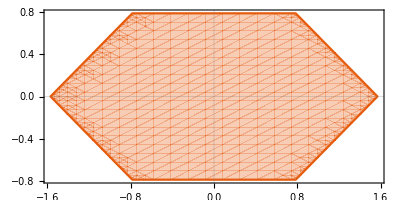

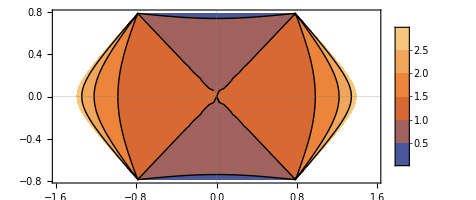

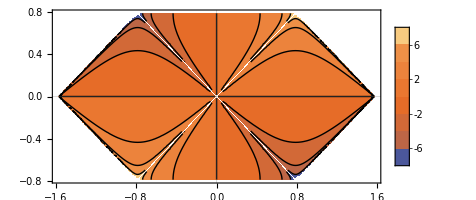

```mathematica
RegionPlot[{Abs[χ+η]<π/2&&Abs[χ-η]<π/2&&1+Cos[2 χ] Sec[2 η]>0&&Abs[χ]≠Abs[η]},{χ,-π/2,π/2},{η,-π/4,π/4},PlotTheme->"Scientific",AspectRatio->Automatic]
ContourPlot[1+ProductLog[-(Tan[η-χ] Tan[η+χ])/ⅇ],{χ,-π/2,π/2},{η,-π/4,π/4},RegionFunction->Function[{χ,η},Tan[η-χ] Tan[η+χ]<1&&Abs[η+χ]<π/2&&Abs[η-χ]<π/2],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
ContourPlot[1/2 Log[(Tan[η+χ]/Tan[η-χ])^2],{χ,-π/2,π/2},{η,-π/4,π/4},RegionFunction->Function[{χ,η},Tan[η-χ] Tan[η+χ]<1&&Abs[η+χ]<π/2&&Abs[η-χ]<π/2],Exclusions->Abs[η]==Abs[χ],PlotLegends->Automatic,PlotTheme->"Scientific",AspectRatio->Automatic]
```

```mathematica
ⅇ^(-ⅈ 2π(t-rstr))/.rstr->r-1+Log[r-1]//FullSimplify
```

ⅇ^(2 ⅈ π (-1+r-t+Log[-1+r]))

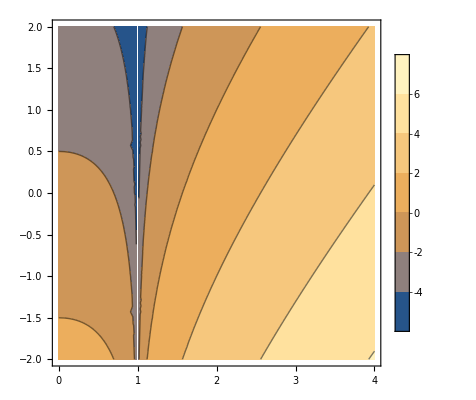

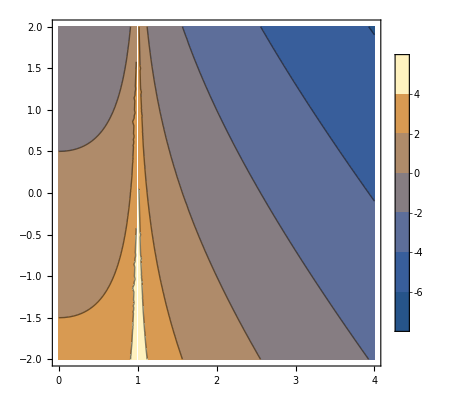

```mathematica
ContourPlot[{-(t-(r-1+Log[Abs[r-1]])+If[r<1,1/2,0])},{r,0,4},{t,-2,2},Exclusions->r==1,PlotLegends->Automatic,AspectRatio->Automatic]
ContourPlot[{-(t+(r-1+Log[Abs[r-1]])+If[r<1,1/2,0])},{r,0,4},{t,-2,2},Exclusions->r==1,PlotLegends->Automatic,AspectRatio->Automatic]
```

```mathematica
2 √Abs[r-1] ⅇ^(-1/2(t-r+1))Piecewise[{{-1, r>1}, {1, 0<r≤1}}]//FullSimplify
```

2 ⅇ^(1/2 (-1+r-t)) √Abs[-1+r] (Piecewise[{{-1, r>1}, {1, 0<r≤1}, {0, True}}])

```mathematica
|
```

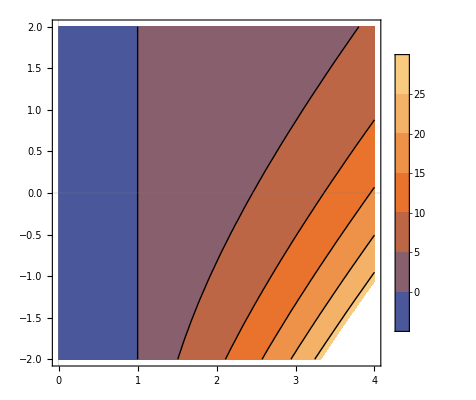

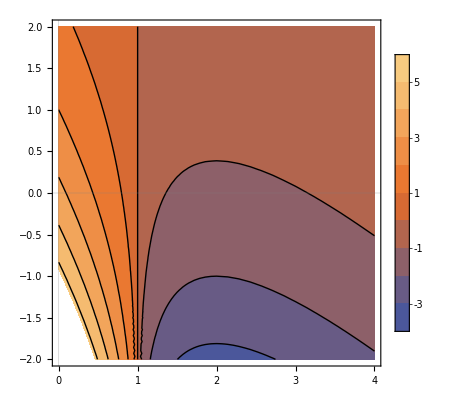

```mathematica
ContourPlot[{-(2 √Abs[r-1] ⅇ^(-1/2(t-r+1))If[r>1,-1,1])},{r,0,4},{t,-2,2},PlotLegends->Automatic,AspectRatio->Automatic,PlotTheme->"Scientific"]
ContourPlot[{-(2 √Abs[r-1] ⅇ^(-1/2(t+r-1))If[r>1,1,-1])},{r,0,4},{t,-2,2},PlotLegends->Automatic,AspectRatio->Automatic,PlotTheme->"Scientific"]
```

```mathematica
(l==#&)/@{1,2}
```

{l==1,l==2}

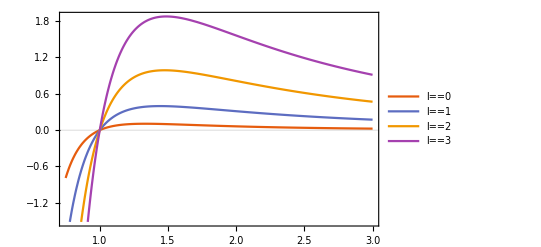

```mathematica
Plot[Table[(1-1/r)(1/r^3+(l(l+1))/r^2),{l,0,3}]//Evaluate,{r,3/4,3},PlotTheme->"Scientific",PlotLegends->(l==#&)/@Range[0,3]]
```